# The Aristotle’s Wheels Paradox

This notebook explore the physics and mathematics behind the paradox of Aristotle’s Wheels

## 1. History of the paradox.

```mathematica
ListAnimate[Import["w.gif"]]
```

This story is about paradox mentioned in the Greek work Mechanica, dubiously attributed to Aristotle. 
Consider a wheel consisting of two concentric circles of different diameters (that is a wheel within a wheel, or a wheel with external axe). Then if we roll this wheel between two straight lines (at the bottom of each of circle) , we can see than the distance developed by a point of the circle with greater diameter is apparently the same than the distance developed by a point on the small circle. So the wheel should travel the same distance regardless of whether it is rolled from left to right on the top straight line or on the bottom one. This seems to imply that the two circumferences of different sized circles are equal, which is impossible and this is the paradox.

We are going to explain the paradox visually coding the draw of graphics step by step.

## 2. Visualization of the paradox .

STEP #1. First of all we draw a simple circle with radius 1 centered at the initial rectangular coordinates C{x_0,y_0} = {0,0}:

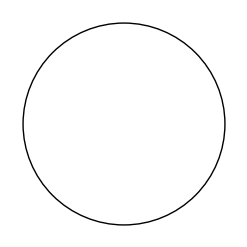

```mathematica
Graphics[Circle[{0,0},1]]
```

STEP #2. After that we mark the center of the circle with a little black disk:

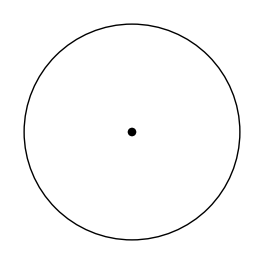

```mathematica
Graphics[{Disk[{0,0},0.04],Circle[{0,0},1]}]
```

STEP #3. Now we draw a small concentric circle with a radius between 0 and 1 than we can manipulate with a control slider:

```mathematica
Manipulate[Graphics[{Disk[{0,0},0.04],Circle[{0,0},1],Circle[{0,0},rsmall]}],{rsmall,0,1,0.1}]
```

STEP #4. We plot two straight lines. One blue at the bottom of the great wheel from (0,-1) to (2π,-1) , and the other red from the bottom of the small wheel from (0,-r_small) to (2π-r_small):

```mathematica
Manipulate[Graphics[{Disk[{0,0},0.04],Circle[{0,0},1],Circle[{0,0},rsmall],Line[{{0,-1},{2 Pi,-1}}],Line[{{0,-rsmall},{2 Pi,-rsmall}}]}],{rsmall,0,1,0.1}]
```

STEP #5. Now we plot the same two wheels at the end of the line and for distinguish them make the first one will be styled with colors and more thick than the second one.

```mathematica
Manipulate[Graphics[{Disk[{0,0},0.04],Style[Circle[{0,0},1],Blue,Thick],Style[Circle[{0,0},rsmall],Red,Thick],Disk[{2Pi,0},0.02],Circle[{2Pi,0},1],Circle[{2Pi,0},rsmall],Line[{{0,-1},{2 Pi,-1}}],Line[{{0,-rsmall},{2 Pi,-rsmall}}]}],{rsmall,0,1,0.1}]
```

STEP #6: We fix the range of plotting and we introduce a new parameter, t, to move the center of the two wheels along the lines:

```mathematica
Manipulate[Graphics[
					{
					Disk[{t,0},0.04],
					Style[Circle[{t,0},1],Blue,Thick],
					Style[Circle[{t,0},rsmall],Red,Thick],
					Disk[{2Pi,0},0.02],
					Circle[{2Pi,0},1],
					Circle[{2Pi,0},rsmall],
					Line[{{0,-1},{2 Pi,-1}}],
					Line[{{0,-rsmall},{2 Pi,-rsmall}}]
					},
				PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}}
				],
			{rsmall,0,1,0.1},{t,0,2Pi}
			]
```

STEP #7: We draw a radial segment of the wheel:

```mathematica
Manipulate[Graphics[
					{
						Disk[{t,0},0.04],
						Style[Circle[{t,0},1],Blue,Thick],
						Style[Circle[{t,0},rsmall],Red,Thick],
						Style[Line[{{t,0},{t,-1}}],Black,Thick],
						Disk[{2Pi,0},0.02],
						Circle[{2Pi,0},1],
						Circle[{2Pi,0},rsmall],
						Line[{{0,-1},{2 Pi,-1}}],
						Line[{{0,-rsmall},{2 Pi,-rsmall}}]
					},
				PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}}
				],
			{rsmall,0,1,0.1},{t,0,2Pi}
			]
```

STEP #8: We rotate the radius of the wheel an angle θ = ω· t , interpreting the parameter t as the time lapsed during the motion and ω as the angular velocity of the wheel while is rolling.

```mathematica
Manipulate[Graphics[
					{
						Disk[{t,0},0.04],
						Style[Circle[{t,0},1],Blue,Thick],
						Style[Circle[{t,0},rsmall],Red,Thick],
						Style[Line[{{t,0},{t-Sin[t],-Cos[t]}}],Black,Thick],
						Disk[{2Pi,0},0.02],
						Circle[{2Pi,0},1],
						Circle[{2Pi,0},rsmall],
						Line[{{0,-1},{2 Pi,-1}}],
						Line[{{0,-rsmall},{2 Pi,-rsmall}}]
					},
				PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}}
				],
			{rsmall,0,1,0.1},{t,0,2Pi}
			]
```

STEP #9: Now we will paint part of the straights lines with blue and red while the wheels are moving rotating around the center. And for a more realistic animation effect we discolour the angular part covered by the radius on the blue and red circles.

```mathematica
Manipulate[Graphics[
					{
						Disk[{t,0},0.04],
						Style[Circle[{t,0},1,{3Pi/2-t,-3Pi/2}],Blue,Thick],
						Style[Circle[{t,0},rsmall,{3Pi/2-t,-3Pi/2}],Red,Thick],
						Style[Line[{{t,0},{t-Sin[t],-Cos[t]}}],Black,Thick],
						Style[Circle[{t,0},1,{3Pi/2,3Pi/2-t}],Black,Thick],
						Style[Circle[{t,0},rsmall,{3Pi/2,3Pi/2-t}],Black,Thick],
						Disk[{2Pi,0},0.02],
						Circle[{2Pi,0},1],
						Circle[{2Pi,0},rsmall],
						Line[{{0,-1},{2 Pi,-1}}],
						Line[{{0,-rsmall},{2 Pi,-rsmall}}],
						Style[Line[{{0,-1},{t,-1}}],Blue,Thick],
						Style[Line[{{0,-rsmall},{t,-rsmall}}],Red,Thick],

					},
				PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}}
				],
			{rsmall,0,1,0.1},{t,0,2Pi}
			]
```

In the animated graphic above we can see it seems than the wheel is rotating, the big circle is travelling the same distance than the smaller circle. But, we know that it is impossible! because the distance traveled by a rotating wheel is given by the expression d = 2 ·π · r, where r is the radius of the wheel. So when the radius of a wheel is smaller than another the distance traveled will be smaller. That is the paradox, and know, coding again, we will expose the explanation of what is really happening with the physical motion of the wheel.

## 3. Explanation of the paradox.

To see what is really happen, first we separate the motion of the blue circle and the red circle when they are rotating at the same angular velocity, but each of them over the bottom an top lines respectively. To do that we introduce a new circle that shadows the smaller circle and that it moves independently of the wheel. 
But previously, we must remember some elementary physics of rotational  kinematics on 2-dimensions:

If a wheel of radius r is rotating over a surface with constant angular velociy ω then the rotating angle described in a time t and measured in radians is given by:

	θ = ω · t

So the length of the arc described by any point at the perimeter of the circle is: 

	d = θ · r = ω · t · r = v · t , where v is the linear velocity of the motion.

If the motion is a pure rotation, then the length of the arc described by the circle must be advanced by the center of the circle on the plane. Consequently, the position of the point P{x_P,y_P} of the wheel initially in contact with the surface, will be given by at any instant of time as a parametric expression depending on t:
			Piecewise[{{x_P[ t ]= x_C[ t ] - r· sin [ θ ] = x_0 + v·t  - r· sin [ θ ]  = ω ·r · t  - r·sin[ ω · t], , where x_C[ t ] = x_0 + v·t   ,indicates the horizontal  position  of the  circle center}, {y_P[ t ] = y_C [t ]  - r · cos [ θ ] = y_0 - r · cos [ ω · t ], , where y_C[ t ] =y_0 , indicates the vertical position  of the  circle center that is constant while the wheel is rotating}}] 

Taking the values {x_0,y_0} = {0,0} and ω = 1, we obtain :

	θ = t
	v = r
	{x_P[ t ]= r · t  - r·sin[ t ]
y_P[ t ] = - r · cos [ t ]

With that equations, now, we can code the simulation of the rotational motion of the red circle:

```mathematica
Manipulate[Graphics[
					{
						(*HERE WE DRAW THE BLUE CIRCLE OF THE WHEEL AND ITS RADIUS*)
						Disk[{t,0},0.04],
						Style[Circle[{t,0},1,{3Pi/2-t,-3Pi/2}],Blue,Thick],
						Style[Line[{{t,0},{t-Sin[t],-Cos[t]}}],Black,Thick],

						(*HERE WE DRAW THE SMALL RED CIRCLE OF THE WHEEL MOVING WITH THE ROTATION OF THE BLUE CIRCLE*)
						Style[Circle[{t,0},rsmall,{3Pi/2-t,-3Pi/2}],Red,Thick],

						(*HERE WE DRAW THE TWO BLACK PARALLEL LINES BETWEEN THE CIRCLES*)
						Line[{{0,-1},{2 Pi,-1}}],
						Line[{{0,-rsmall},{2 Pi,-rsmall}}],
																						
						(*HERE WE DRAW THE WHEEL IN ITS FINAL POSITION AFTER A COMPLETE TURN ROTATING OVER THE BOTTOM LINE*)
						Disk[{2Pi,0},0.02],
						Circle[{2Pi,0},1],
						Circle[{2Pi,0},rsmall],
						
						(*HERE WE DRAW IN BLACK THE CIRCLE ARCS COVERED DURING THE ROTATION OF THE WHEEL*)
						Style[Circle[{t,0},1,{3Pi/2,3Pi/2-t}],Black,Thick],
						Style[Circle[{t,0},rsmall,{3Pi/2,3Pi/2-t}],Black,Thick],
						
						(*HERE WE DRAW IN BLUE AND RED THE EQUIVALENT WALKING DISTANCE OF THE WHEEL OVER THE LINES*)
						Style[Line[{{0,-1},{t,-1}}],Blue,Thick],
						Style[Line[{{0,-rsmall},{t,-rsmall}}],Red,Thick],
						
						(*HERE WE DRAW AN INDEPENDENT SMALL RED CIRCLE OF THE WHEEL ROTATING WITH THE ANGULAR VELOCITY OF THE BLUE CIRCLE*)
						Disk[{rsmall*t,0},0.04],
						Style[Circle[{rsmall*t,0},rsmall],Red],
						Style[Line[{{rsmall*t,0},{rsmall*t - rsmall*Sin[t], -rsmall*Cos[t]}}],Black],
					},
				PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}}
				],
			
			{rsmall,0,1,0.1},{t,0,2Pi}
			]
```

In conclusion we can deduce that the inner circle of the wheel is not describing a pure rotation over the top line, because is it was rotating the red walking distance would be shorter than the blue one (as we can see observing the motion of the the outside small red circle). But if the inner red circle is not rotating, how kind of motion is doing?

To answer that last question we are going to plot the trajectory of the points of contact with the lines of the different circles:

```mathematica
Manipulate[
		Show[{
			(*HERE WE PLOT THE PARAMETRIC TRAJECTORIES THAT TRACES FROM THEIR INITIAL POSTIONS EACH OF THE CONTACTS POINTS*)
			(*TRAJECTORY OF THE BLUE CIRCLE POINT f[{x[u],y[u]}]={u-Sin[u],-Cos[u]}]*)
			ParametricPlot[
						{u-Sin[u],-Cos[u]},
						{u,10^-9,t},
						AxesOrigin->{0,0},
						PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}},
						PlotStyle->Blue,
						Ticks->None
						],
			(*TRAJECTORY OF THE EXTERNAL RED CIRCLE POINT f[{x[u],y[u]}]={rsmall*u-rsmall*Sin[u],-rsmall*Cos[u]}]*)
			ParametricPlot[
						{rsmall*u-rsmall*Sin[u],-rsmall*Cos[u]},
						{u,10^-9,t},
						AxesOrigin->{0,0},
						PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}},
						PlotStyle->Red,Ticks->None
						],
			(*TRAJECTORY OF THE INNER RED CIRCLE POINT f[{x[u],y[u]}]={u-rsmall*Sin[u],-rsmall*Cos[u]}]*)
			ParametricPlot[
						{u-rsmall*Sin[u],-rsmall*Cos[u]},
						{u,10^-9,t},
						AxesOrigin->{0,0},
						PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}},
						PlotStyle->Green,Ticks->None
						],
			Graphics[
					{
						(*HERE WE DRAW THE BLUE CIRCLE OF THE WHEEL AND ITS RADIUS*)
						Disk[{t,0},0.04],
						Style[Circle[{t,0},1,{3Pi/2-t,-3Pi/2}],Blue,Thick],
						Style[Line[{{t,0},{t-Sin[t],-Cos[t]}}],Black,Thick],

						(*HERE WE DRAW THE SMALL RED CIRCLE OF THE WHEEL MOVING WITH THE ROTATION OF THE BLUE CIRCLE*)
						Style[Circle[{t,0},rsmall,{3Pi/2-t,-3Pi/2}],Red,Thick],

						(*HERE WE DRAW THE TWO BLACK PARALLEL LINES BETWEEN THE CIRCLES*)
						Line[{{0,-1},{2 Pi,-1}}],
						Line[{{0,-rsmall},{2 Pi,-rsmall}}],
																						
						(*HERE WE DRAW THE WHEEL IN ITS FINAL POSITION AFTER A COMPLETE TURN ROTATING OVER THE BOTTOM LINE*)
						Disk[{2Pi,0},0.02],
						Circle[{2Pi,0},1],
						Circle[{2Pi,0},rsmall],
						
						(*HERE WE DRAW IN BLACK THE CIRCLE ARCS COVERED DURING THE ROTATION OF THE WHEEL*)
						Style[Circle[{t,0},1,{3Pi/2,3Pi/2-t}],Black,Thick],
						Style[Circle[{t,0},rsmall,{3Pi/2,3Pi/2-t}],Black,Thick],
						
						(*HERE WE DRAW IN BLUE AND RED THE EQUIVALENT WALKING DISTANCE OF THE WHEEL OVER THE LINES*)
						Style[Line[{{0,-1},{t,-1}}],Blue,Thick],
						Style[Line[{{0,-rsmall},{t,-rsmall}}],Red,Thick],
						
						(*HERE WE DRAW AN INDEPENDENT SMALL RED CIRCLE OF THE WHEEL ROTATING WITH THE ANGULAR VELOCITY OF THE BLUE CIRCLE*)
						Disk[{rsmall*t,0},0.04],
						Style[Circle[{rsmall*t,0},rsmall],Red],
						Style[Line[{{rsmall*t,0},{rsmall*t - rsmall*Sin[t], -rsmall*Cos[t]}}],Black],
						},
					PlotRange->{{-1.1,1.1+2Pi},{-1.1,1.1}}
				]
		}],
			{{rsmall,2,"radius"},0,1,0.1},{{t,2,"time"},0,2Pi}
		]
```

After visualizing that, we can see clearly that the blue and red trajectories are cycloid (the common form of the family of trochoid curves), but the green curve is a curtate trochoid so it’s no correspond to a pure rotating motion. In conclusion if we force the wheel to rolling purely over the bottom line, the motion of the inner circle is not a rolling motion, it’s must be a mixing of sliding and rotating motion along the top line.

## Conclusions

Wikipedia: https://en.wikipedia.org/wiki/Aristotle%27 s_wheel _paradox
Wolfram MathWorld: http://mathworld.wolfram.com/AristotlesWheelParadox.html
Wolfram Demonstration Project: http://demonstrations.wolfram.com/CycloidCurves/

## References

Wikipedia: https://en.wikipedia.org/wiki/Aristotle%27 s_wheel _paradox
Wolfram MathWorld: http://mathworld.wolfram.com/AristotlesWheelParadox.html
Wolfram Demonstration Project: http://demonstrations.wolfram.com/CycloidCurves/

## Related Topics

Physics
	Mechanics
	Kinematics
	Circular motion
Mathematics
	Geometry
	Circumference
	Cycloid
	Trochoid
Philosophy
	Aristotle
	Paradox

Further Explorations

In next explorations it would be interesting to code with functions of colors the different kinds of motion (rolling and sliding) of the wheels for a better visualization of the paradox. A second exploration would be improve the structure of the code and the draw functions used to generalize and at the same time make more clear all the explanation.

Authorship information

Mariano Cano Santos
Institut Sòl-de-Riu
Department of Mathematics
http://institutsolderiu.cat

Code developed as a topic exploration during the Wolfram Summer School 2017
Bentley University, Waltham, MA June 18–July 7, 2017

email: mcanosan@gmail.com